# Demonstration

A concise demonstration of the ultimate calculation performed in tutorial.nb

Get the QuEST Mathematica package

```mathematica
Import["https://quest.qtechtheory.org/QuEST.m"]
```

Download and connect to a local MacOS QuEST runtime environment

```mathematica
env = CreateDownloadedQuESTEnv[];
```

Allocate a 9 qubit state vector and density matrix

```mathematica
numQb = 9;
ψ = CreateQureg[numQb];
ρ = CreateDensityQureg[numQb];
```

Specify a 9 qubit circuit, which includes decoherence of strength parameterized by θ

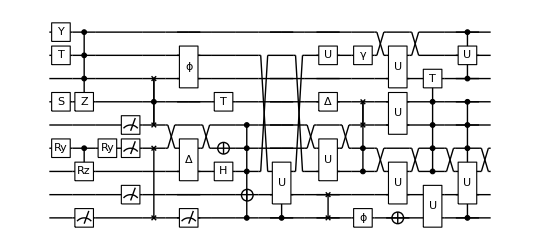

```mathematica
m1 = ({{0, ⅈ}, {Exp[.3ⅈ], 0}});
m2 = ({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});

u[θ_]:= Circuit[
 Subscript[S, 5] Subscript[T, 7] Subscript[Y, 8] Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]]Subscript[C, 8,7,6][Subscript[Z, 5]] Subscript[M, 0] Subscript[Ry, 3][θ] Subscript[M, 1,3,4] Subscript[SWAP, 0,3] Subscript[C, 5][Subscript[SWAP, 4,6]]Subscript[Depol, 2,4][θ/100] Subscript[Deph, 7,6][θ/400] Subscript[M, 0] Subscript[H, 2] Subscript[X, 3] Subscript[T, 5] Subscript[C, 0,2,3,4][Subscript[X, 1]] Subscript[C, 0][Subscript[U, 1,7][m2]]Subscript[U, 2,4][m2] Subscript[U, 7][m1]  Subscript[SWAP, 0,1] Subscript[Depol, 5][θ/300] Subscript[Deph, 0][θ/200]   Subscript[Damp, 7][θ/500] Subscript[C, 2,3][Subscript[SWAP, 4,5]] Subscript[U, 3,1][m2] Subscript[U, 4,5][m2] Subscript[U, 6,8][m2] Subscript[X, 0]  Subscript[U, 0,1][m2] Subscript[C, 2,3,4,5][Subscript[T, 6]] Subscript[C, 0,2,4,5][Subscript[U, 1,3][m2]]Subscript[C, 6,8][Subscript[U, 7][m1]] 
];

DrawCircuit @ u[θ]
```

Compute how smoothly varying θ affects the fidelity against the noise-free state.

```mathematica
ApplyCircuit[u[0],InitPlusState @ ψ];

params = Range[0,π,.01];
fids = Table[
	ApplyCircuit[u[θ],InitPlusState @ ρ];
	CalcFidelity[ρ, ψ],
	{θ, params}
];
```

Note the results here are random since our circuit contains projective measurement gates.

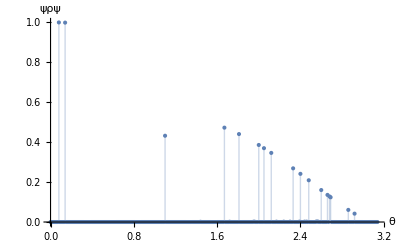

```mathematica
ListPlot[
	Transpose[{params,fids}], 
	AxesLabel-> {"θ","ψρψ"},
	Filling->Bottom
]
```

Free QuEST memory and disconnect from QUEST environment

```mathematica
DestroyAllQuregs[]; 
DestroyQuESTEnv[env];
```